# Quantum Fourier Transform

XXXX.

The quantum Fourier transform algorithm is illustrated in a circuit.

```mathematica
<<Q3`Quisso`
```

```mathematica
Let[Qubit,S]
```

```mathematica
nn=Range[5];
qq=S[nn,]
```

{S_1,S_2,S_3,S_4,S_5}

```mathematica
CR[m_,n_,k_]:=ControlledU[S[m],Phase[2Pi/2^k,S[n]],Label->Subscript["R",m]]
```

```mathematica
Let[Integer,j]
Clear[v]
jj=j[nn];
jj=Ket/@jj;
v[1]=LogicalForm[Ket[],qq];
```

```mathematica
phase[k_]:=With[
{jj=j[nn]},
Row[{Ket[0],"+",Ket[1],Superscript["e",Row@Join[{"2π"," i ","0","."},Drop[jj,k-1]]]}]
]
ll=Array[phase,5]
v[2]=ProductState[S[nn]->{1,0}]
```

{0+1e^(2π i 0.j_1j_2j_3j_4j_5),0+1e^(2π i 0.j_2j_3j_4j_5),0+1e^(2π i 0.j_3j_4j_5),0+1e^(2π i 0.j_4j_5),0+1e^(2π i 0.j_5)}

(0)_S_1⊗(0)_S_2⊗(0)_S_3⊗(0)_S_4⊗(0)_S_5

Recall that unlike the seemingly general label, the example below is for a particular input.

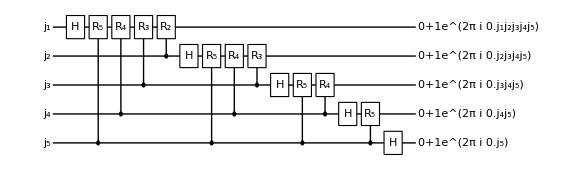

```mathematica
qc=QuissoCircuit[
{v[1],Label->jj},
S[1,6],CR[5,1,5],CR[4,1,4],CR[3,1,3],CR[2,1,2],
S[2,6],CR[5,2,4],CR[4,2,3],CR[3,2,2],
S[3,6],CR[5,3,3],CR[4,3,2],
S[4,6],CR[5,4,2],
S[5,6],
{v[2],Label->ll},
ImageSize->Large,
PlotRangePadding->{2,0}]
```

```mathematica
Timing[QuissoExpression[qc]//Simplify//LogicalForm[#,qq]&]
```

{0.263948,1/(4 √2)(0_S_10_S_20_S_30_S_40_S_5+0_S_10_S_20_S_30_S_41_S_5+0_S_10_S_20_S_31_S_40_S_5+0_S_10_S_20_S_31_S_41_S_5+0_S_10_S_21_S_30_S_40_S_5+0_S_10_S_21_S_30_S_41_S_5+0_S_10_S_21_S_31_S_40_S_5+0_S_10_S_21_S_31_S_41_S_5+0_S_11_S_20_S_30_S_40_S_5+0_S_11_S_20_S_30_S_41_S_5+0_S_11_S_20_S_31_S_40_S_5+0_S_11_S_20_S_31_S_41_S_5+0_S_11_S_21_S_30_S_40_S_5+0_S_11_S_21_S_30_S_41_S_5+0_S_11_S_21_S_31_S_40_S_5+0_S_11_S_21_S_31_S_41_S_5+1_S_10_S_20_S_30_S_40_S_5+1_S_10_S_20_S_30_S_41_S_5+1_S_10_S_20_S_31_S_40_S_5+1_S_10_S_20_S_31_S_41_S_5+1_S_10_S_21_S_30_S_40_S_5+1_S_10_S_21_S_30_S_41_S_5+1_S_10_S_21_S_31_S_40_S_5+1_S_10_S_21_S_31_S_41_S_5+1_S_11_S_20_S_30_S_40_S_5+1_S_11_S_20_S_30_S_41_S_5+1_S_11_S_20_S_31_S_40_S_5+1_S_11_S_20_S_31_S_41_S_5+1_S_11_S_21_S_30_S_40_S_5+1_S_11_S_21_S_30_S_41_S_5+1_S_11_S_21_S_31_S_40_S_5+1_S_11_S_21_S_31_S_41_S_5)}